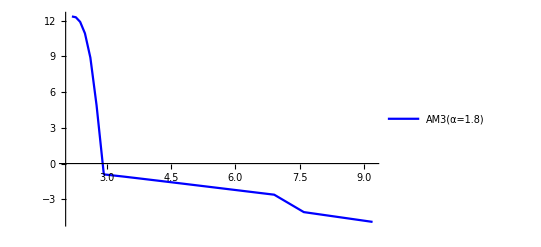

```mathematica
data={
{-Log[0.114],Log[10,2305975474491.8583984]},
{-Log[0.104],Log[10,1971918046975.9541016]},
{-Log[0.094],Log[10,808682717070.50158691]},
{-Log[0.084],Log[10,87074560342.633148193]},
{-Log[0.074],Log[10,797809827.79695928097]},
{-Log[0.064],Log[10,77448.808833130315179]},
{-Log[0.054],Log[10,0.12315036854422632684]},
{-Log[0.044],Log[10,0.10187587143850675153]},
{-Log[0.034],Log[10,0.080464185229975351832]},
{-Log[0.024],Log[10,0.057342421751820464582]},
{-Log[0.014],Log[10,0.033709032595991103576]},
{-Log[0.01],Log[10,0.024122478771761195898]},
{-Log[0.005],Log[10,0.012077702410035874234]},
{-Log[0.001],Log[10,0.0024166147036476588912]},
{-Log[0.0005],Log[10,8.3179420601194813401*10^-5]},
{-Log[0.0001],Log[10,1.2512734557379445732*10^-5]}

};
p1=ListLinePlot[data,Joined->True,PlotStyle->Blue,PlotLegends->{"AM3(α=1.8)"}]
```

OptionValue::nodef: Graphics 的未知选项 Image.

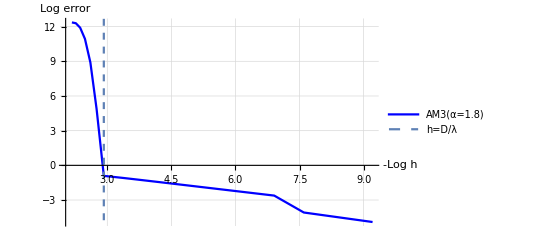

```mathematica
Show[p1,ParametricPlot[{-Log[0.054],t},{t,-15,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

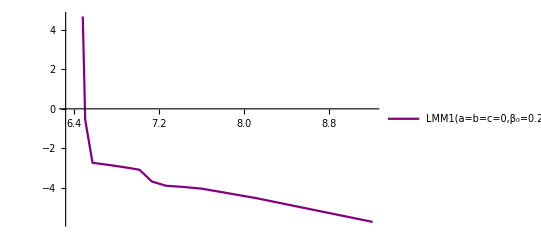

```mathematica
data1={
{-Log[0.0001],Log[10,1.7856192254139813258*10^-6]},
{-Log[0.0003],Log[10,2.8968733037926241991*10^-5]},
{-Log[0.0005],Log[10,8.7388385525355438688*10^-5]},
{-Log[0.0006],Log[10,0.0001078542527008785612]},
{-Log[0.0007],Log[10,0.00012257830975686111685]},
{-Log[0.0008],Log[10,0.00020170187877766032614]},
{-Log[0.0009],Log[10,0.00080000534950358439396]},
{-Log[0.001],Log[10,0.0010000061088868375959]},
{-Log[0.0011],Log[10,0.0012000063294590110601]},
{-Log[0.0012],Log[10,0.0014000062547813998341]},
{-Log[0.0013],Log[10,0.0016000058408804686012]},
{-Log[0.0014],Log[10,0.0018000058498712366746]},
{-Log[0.0015],Log[10,0.2775801596733605825]},
{-Log[0.0016],Log[10,198104157080290.875]},
{-Log[0.0017],Log[10,1.5646178608905480707*E^26]}};

p3=ListLinePlot[data1,Joined->True,PlotStyle->Purple,PlotLegends->{"LMM1(a=b=c=0,β_0=0.25)"}]
```

```mathematica
|
```

OptionValue::nodef: Graphics 的未知选项 Image.

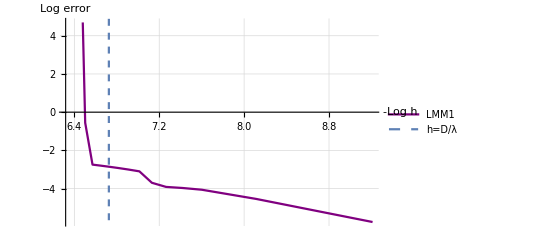

```mathematica
Show[p3,ParametricPlot[{-Log[0.0012],t},{t,-20,20},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log error]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

OptionValue::nodef: Graphics 的未知选项 Image.

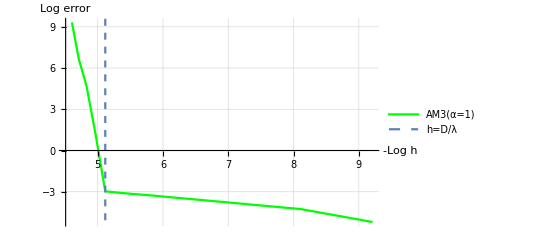

```mathematica
data7={
{-Log[0.01],Log[10,2079787412.4869394302]},
{-Log[0.009],Log[10,4540376.5577806066722]},
{-Log[0.008],Log[10,50456.822026708221529]},
{-Log[0.007],Log[10,21.416129917749415768]},
{-Log[0.006],Log[10,0.0010742889188091186981]},
{-Log[0.005],Log[10,0.0008684828684308865121]},
{-Log[0.004],Log[10,0.00069781317142370014039]},
{-Log[0.003],Log[10,0.0005437069199207833492]},
{-Log[0.002],Log[10,0.00036247127897670594621]},
{-Log[0.001],Log[10,0.00018161073487843459873]},
{-Log[0.0005],Log[10,9.0805367418456128803*10^-5]},
{-Log[0.0003],Log[10,5.4471970030278704655*10^-5]},
{-Log[0.0001],Log[10,6.26366524125732127*10^-6]}};
p19=ListPlot[data7,Joined->True,PlotStyle->Green,PlotLegends->{"AM3(α=1)"}];
Show[p19,ParametricPlot[{-Log[0.006],t},{t,-40,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

OptionValue::nodef: Graphics 的未知选项 Image.

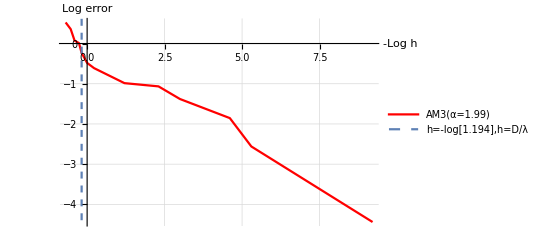

```mathematica
data8={{-Log[2],Log[10,3.3436756549351618339]},
{-Log[1.7],Log[10,2.2830124541437628594]},
{-Log[1.5],Log[10,1.1835858957732927621]},
{-Log[1.3],Log[10,1.0223419979144277026]},
{-Log[1.194],Log[10,0.5818367401224151525]},
{-Log[1],Log[10,0.32912524498085138358]},
{-Log[0.8],Log[10,0.24442890717491827512]},
{-Log[0.3],Log[10,0.10347783199823906708]},
{-Log[0.1],Log[10,0.085961596380856764021]},
{-Log[0.05],Log[10,0.041702269476535380743]},
{-Log[0.01],Log[10,0.013967126418871433913]},
{-Log[0.005],Log[10,0.0027552371773359451979]},
{-Log[0.0001],Log[10,3.6447282555029936191*10^-5]}};
p20=ListPlot[data8,Joined->True,PlotStyle->Red,PlotLegends->{"AM3(α=1.99)"}];
Show[p20,ParametricPlot[{-Log[1.194],t},{t,-40,30},PlotStyle->Dashed,PlotLegends->{"h=-log[1.194],h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

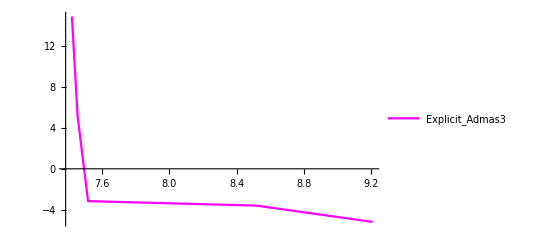

OptionValue::nodef: Graphics 的未知选项 Image.

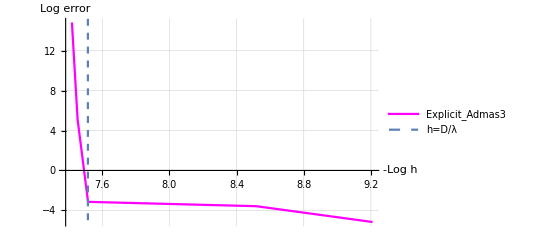

```mathematica
data9={
{-Log[0.0006],Log[10,679050610893288.125]},
{-Log[0.00058],Log[10,130394.61694029028877]},
{-Log[0.000545],Log[10,0.0007134239268916653387]},
{-Log[0.0005],Log[10,0.00065481091319652406924]},
{-Log[0.0004],Log[10,0.00052347084866521953472]},
{-Log[0.0003],Log[10,0.00039256265363118991729]},
{-Log[0.0002],Log[10,0.00026168144455884778665]},
{-Log[0.0001],Log[10,6.7944189917623631914*10^-6]}};
p21=ListLinePlot[data9,Joined->True,PlotStyle->Magenta,PlotLegends->{"Explicit_Admas3"}]
Show[p21,ParametricPlot[{-Log[0.00054545454],t},{t,-40,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

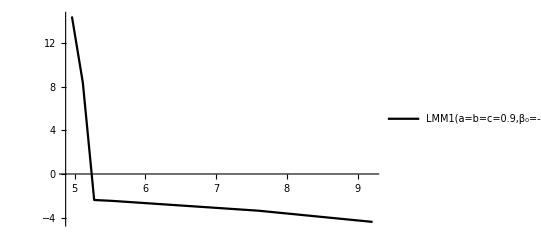

OptionValue::nodef: Graphics 的未知选项 Image.

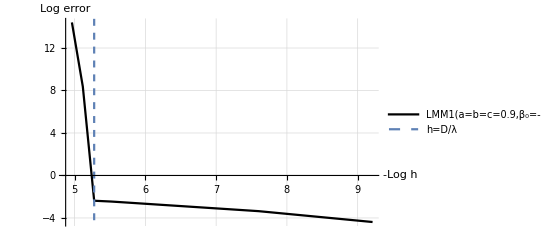

```mathematica
data10={{-Log[0.007],Log[10,255641590656558.59375]},
{-Log[0.006],Log[10,232407194.25766155124]},
{-Log[0.00511],Log[10,0.0041788258369820363569]},
{-Log[0.004],Log[10,0.0034941516895010682475]},
{-Log[0.003],Log[10,0.0026260024171890217204]},
{-Log[0.002],Log[10,0.0017470659498332041792]},
{-Log[0.001],Log[10,0.00087353157266656378255]},
{-Log[0.0005],Log[10,0.0004363157723659139009]},
{-Log[0.0001],Log[10,4.149635701866660753*10^-5]}};
p22=ListLinePlot[data10,Joined->True,PlotStyle->Black,PlotLegends->{"LMM1(a=b=c=0.9,β_0=-0.2)"}]
Show[p22,ParametricPlot[{-Log[41154/(8051*1000)],t},{t,-40,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

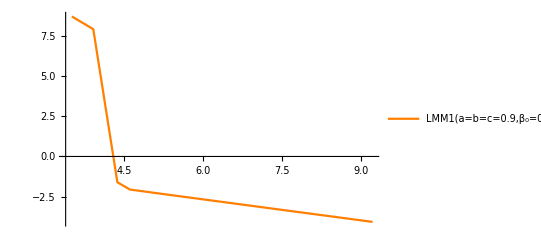

OptionValue::nodef: Graphics 的未知选项 Image.

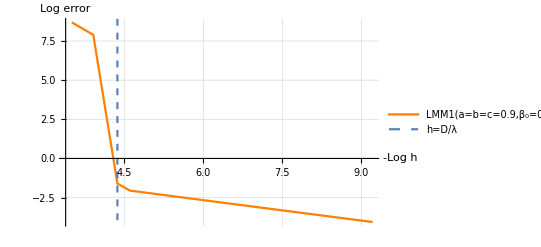

```mathematica
data11={
{-Log[0.03],Log[10,487025493.47279906273]},
{-Log[0.02],Log[10,78684687.977292940021]},
{-Log[0.012659],Log[10,0.025113766508967350077]},
{-Log[0.01],Log[10,0.0089041904149841366589]},
{-Log[0.005],Log[10,0.0043946866455709665544]},
{-Log[0.001],Log[10,0.0008735317662860175858]},
{-Log[0.0005],Log[10,0.00043631579665548425595]},
{-Log[0.0001],Log[10,8.7191157263966090341*10^-5]}};
p23=ListLinePlot[data11,Joined->True,PlotStyle->Orange,PlotLegends->{"LMM1(a=b=c=0.9,β_0=0)"}]
Show[p23,ParametricPlot[{-Log[41154/(3251*1000)],t},{t,-40,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

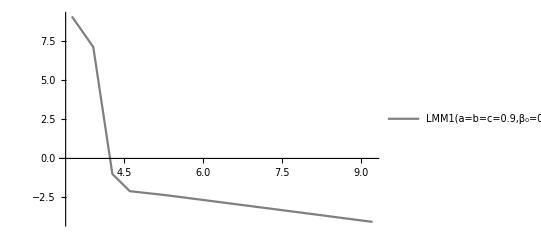

OptionValue::nodef: Graphics 的未知选项 Image.

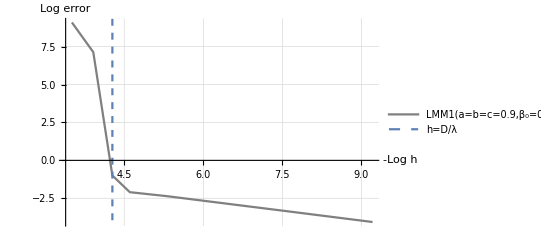

```mathematica
data12={
{-Log[0.03],Log[10,1250195494.331818819]},
{-Log[0.02],Log[10,13723996.370425501838]},
{-Log[0.0139252],Log[10,0.10043986079451772131]},
{-Log[0.01],Log[10,0.0079618824437589497123]},
{-Log[0.005],Log[10,0.004395257778540218041]},
{-Log[0.001],Log[10,0.00087353175509219394002]},
{-Log[0.0005],Log[10,0.00043631579520631014191]},
{-Log[0.0001],Log[10,8.5820700633121305145*10^-5]}};
p24=ListLinePlot[data12,Joined->True,PlotStyle->Gray,PlotLegends->{"LMM1(a=b=c=0.9,β_0=0.012318)"}]
Show[p24,ParametricPlot[{-Log[13.9251693866889/1000],t},{t,-40,30},PlotStyle->Dashed,PlotLegends->{"h=D/λ"}],GridLines->Automatic,AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},Image->Large,LabelStyle->{12,GrayLevel[0]},Image->Large,LabelStyle->{12,GrayLevel[0]}]
```

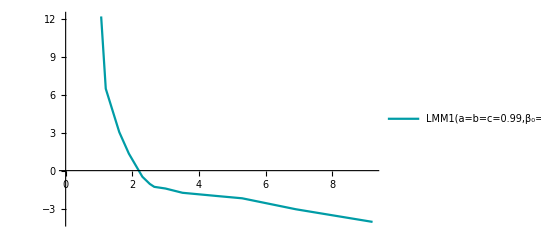

```mathematica
data30={
{-Log[0.5],Log[940385261232.28149414]},
{-Log[0.3],Log[10,3066216.3110795835964]},
{-Log[0.2],Log[10,1117.9322410210909311]},
{-Log[0.15],Log[10,22.217265324127161819]},
{-Log[0.1],Log[10,0.32782027494085408392]},
{-Log[0.08],Log[10,0.088421061163369785163]},
{-Log[0.07],Log[10,0.052028565733908793689]},
{-Log[0.05],Log[10,0.038342819516704707006]},
{-Log[0.03],Log[10,0.017594437891838565768]},
{-Log[0.01],Log[10,0.0094415572053520024909]},
{-Log[0.005],Log[10,0.0064420198079504498168]},
{-Log[0.001],Log[10,0.00087425502655469333746]},
{-Log[0.0005],Log[10,0.00043597939944073349494]},
{-Log[0.0001],Log[10,8.7192952069714557695*10^-5]}
};
p30=ListLinePlot[data30,Joined->True,PlotStyle->RGBColor[0.,0.61,0.65],PlotLegends->{"LMM1(a=b=c=0.99,β_0=0.000147)"}]
```

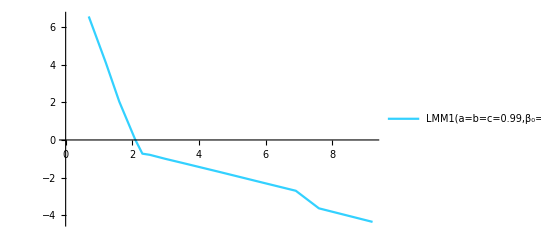

```mathematica
data31={
{-Log[0.5],Log[10,3616256.5832540071569]},
{-Log[0.3],Log[10,12897.342460153344291]},
{-Log[0.2],Log[10,108.40894514391199266]},
{-Log[0.1243],Log[10,1.0782062548367603583]},
{-Log[0.1],Log[10,0.1872733268380222249]},
{-Log[0.08],Log[10,0.16239230963222814341]},
{-Log[0.05],Log[10,0.098964884646848688687]},
{-Log[0.03],Log[10,0.060179736656419895169]},
{-Log[0.01],Log[10,0.020276499600199133361]},
{-Log[0.005],Log[10,0.010080023573545888321]},
{-Log[0.003],Log[10,0.006017625849147542616]},
{-Log[0.001],Log[10,0.0020002853032648087485]},
{-Log[0.0005],Log[10,0.00023372741743219478394]},
{-Log[0.0001],Log[10,4.4557546518638773136*10^-5]}

};
p31=ListLinePlot[data31,Joined->True,PlotStyle->RGBColor[0.2,0.82,1.],PlotLegends->{"LMM1(a=b=c=0.99,β_0=-0.001)"}]
```

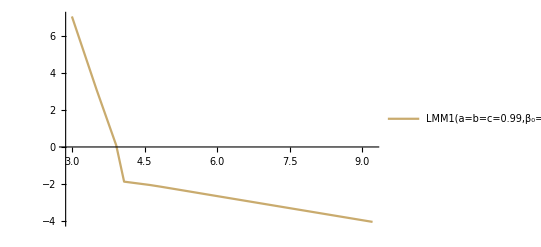

```mathematica
data32={
{-Log[0.05],Log[10,11762842.272093584761]},
{-Log[0.03],Log[10,1247.6032876690064768]},
{-Log[0.02],Log[10,1.2255018714852763395]},
{-Log[0.017],Log[10,0.013214668858674505358]},
{-Log[0.01],Log[10,0.008726114578885280082]},
{-Log[0.008],Log[10,0.0070673203564971531776]},
{-Log[0.005],Log[10,0.0044068693064823749594]},
{-Log[0.003],Log[10,0.0026319016570645059616]},
{-Log[0.001],Log[10,0.00087419870653959730333]},
{-Log[0.0005],Log[10,0.00043641743973177327121]},
{-Log[0.0001],Log[10,8.7192988881379385191*10^-5]}

};
p32=ListLinePlot[data32,Joined->True,PlotStyle->RGBColor[0.79,0.67,0.43],PlotLegends->{"LMM1(a=b=c=0.99,β_0=-0.1)"}]
```

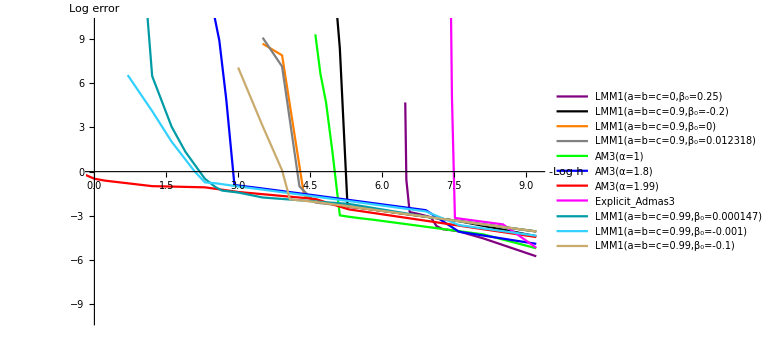

```mathematica
Show[p3,p22,p23,p24,p19,p1,p20,p21,p30,p31,p32,PlotRange->{{0,9.2},{-10,10}},LabelStyle->{12,GrayLevel[0]},AxesLabel->{HoldForm[-Log(h)],HoldForm[Log(error)]},ImageSize->Large,AxesOrigin->{0,0}]
```

```mathematica
Subscript[β, 0]
```